```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<PlotOption`
```

## Exercise

```mathematica
OscillationData=Import["oscillation.dat"];
```

```mathematica
xList=Map[{#[[1]],#[[2]]}&,OscillationData];
```

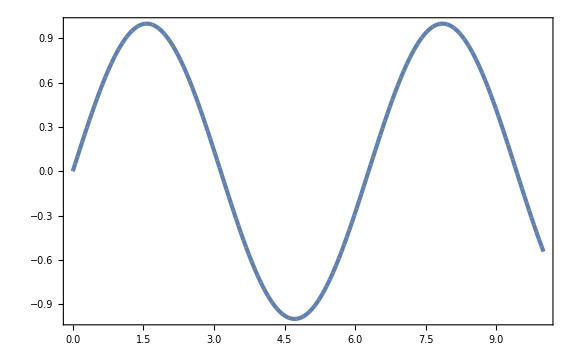

```mathematica
Show[ListPlot[xList],Plot[Sin[x],{x,0,10},PlotStyle->{Color[2],Dotted}]]
```